# Seven Circles Theorem

### Author

Eric W. Weisstein
November 10, 2004

This notebook downloaded from http://mathworld.wolfram.com/notebooks/PlaneGeometry/SevenCirclesTheorem.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/SevenCirclesTheorem.html.

©2005 Wolfram Research, Inc. except for portions noted otherwise

```mathematica
SevenCircles::usage="SevenCircles[r,n] gives the seven circles theorem for the circles with the 6 specified radii (the seventh is computed from these six).  n=-1 makes the first circle external, n=1 makes all circles around the first one."

SevenCirclesPoint::usage="SevenCirclesPoint[r] gives the point of intersection in the SevenCircles figure."

SevenCirclesTriangle::usage="SevenCirclesTriangle[r] gives the Seven Circles triangle figure."

SevenCirclesTrianglePoint::usage="SevenCirclesTrianglePoint[r] gives the Seven Circles triangle point of concurrence."
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
(*Seven Circles*)
```

```mathematica
c7[1,n_Integer,r_List]:={0,0}

c7[2,n_Integer,r_List]:={r[[1]]+n r[[2]],0}

c7[3,n_,r_List]:=c7[3,n,r]=Module[{xx,yy},Select[{xx,yy}/.Solve[{(xx-x[1,n,r])^2+(yy-y[1,n,r])^2==(r[[1]]+n r[[3]])^2,(xx-x[2,n,r])^2+(yy-y[2,n,r])^2==(r[[2]]+r[[3]])^2},{xx,yy}],#[[2]]>0&][[1]]];

x[n_,m_,r_List]:=c7[n,m,r][[1]]

y[n_,m_,r_List]:=c7[n,m,r][[2]]

circ[7,n_,r_List]:=circ[7,n,r]=Module[{xx,yy,rr},Select[Circle[{xx,yy},rr]/.Solve[{(xx-x[2,n,r])^2+(yy-y[2,n,r])^2==(r[[2]]+rr)^2,(xx-x[6,n,r])^2+(yy-y[6,n,r])^2==(r[[6]]+rr)^2,(xx-x[1,n,r])^2+(yy-y[1,n,r])^2==(r[[1]]+n rr)^2},{xx,yy,rr}],#[[2]]>0&][[1]]]

circ[n_,m_,r_List]:=circ[n,m,r]=Circle[c7[n,m,r],r[[n]]];

c7[n_,m_,r_List]:=c7[n,m,r]=Module[{xx,yy,s,k=2-(m+1)/2},s={xx,yy}/.Solve[{(xx-x[n-1,m,r])^2+(yy-y[n-1,m,r])^2==(r[[n-1]]+r[[n]])^2,(xx-x[k,m,r])^2+(yy-y[k,m,r])^2==(r[[n]]+r[[k]])^2},{xx,yy}];
Select[s,(#[[1]]-x[k,m,r])(y[n-1,m,r]-y[k,m,r])-(#[[2]]-y[k,m,r])(x[n-1,m,r]-x[k,m,r])<0&][[1]]]

u[r_List,n_,i_,j_:2]:=c7[i,n,r]-(c7[i,n,r]-c7[j,n,r])/Sqrt[(c7[i,n,r]-c7[j,n,r]).(c7[i,n,r]-c7[j,n,r])]r[[i]]

seg[1,-1,r_List]:={{r[[1]],0},u[r,-1,5]}

seg[2,-1,r_List]:={u[r,-1,3],u[r,-1,6]}

seg[3,-1,r_List]:={u[r,-1,4],u[r,-1,7]}

seg[1,1,r_List]:={u[r,1,2,1],u[r,1,5,1]}

seg[2,1,r_List]:={u[r,1,3,1],u[r,1,6,1]}

seg[3,1,r_List]:={u[r,1,4,1],u[r,1,7,1]}

SevenCirclesPoint[r_List,n_]:=RegionIntersection[Line@seg[1,n,r],Line@seg[2,n,r]]

SevenCircles[r0_List,n_]:=Module[{i,r=Append[r0,circ[7,n,r0][[2]]]},{Table[Line[seg[i,n,r]],{i,3}],Table[circ[i,n,r],{i,7}]}]

SevenCirclesTriangle[t_List]:=Module[{in=Incircle[t],c,i},c=CornerCircles[{{in[[1,1]],in[[1,2]]},in[[2]]},t];
ct=ContactTriangle[t][[1]];
{Triangle[t],Incircle[t],c,Line[{{ct[[1]]},{c[[2,1]]+c[[2,2]](ct[[1]]-c[[2,1]])/Sqrt[(ct[[1]]-c[[2,1]]).(ct[[1]]-c[[2,1]])]}}],Line[{{ct[[2]]},{c[[1,1]]+c[[1,2]](ct[[2]]-c[[1,1]])/Sqrt[(ct[[2]]-c[[1,1]]).(ct[[2]]-c[[1,1]])]}}],Line[{{ct[[3]]},{c[[3,1]]+c[[3,2]](ct[[3]]-c[[3,1]])/Sqrt[(ct[[3]]-c[[3,1]]).(ct[[3]]-c[[3,1]])]}}]}]
SevenCirclesTrianglePoint[t_List]:=Module[{in=Incircle[t],c,i},c=CornerCircles[{{in[[1,1]],in[[1,2]]},in[[2]]},t];
ct=ContactTriangle[t][[1]];
RegionIntersection[Line@{{ct[[1]]},{c[[2,1]]+c[[2,2]](ct[[1]]-c[[2,1]])/Sqrt[(ct[[1]]-c[[2,1]]) (ct[[1]]-c[[2,1]])]}},Line@{{ct[[2]]},{c[[1,1]]+c[[1,2]](ct[[2]]-c[[1,1]])/Sqrt[(ct[[2]]-c[[1,1]])  (ct[[2]]-c[[1,1]])]}}]]
```

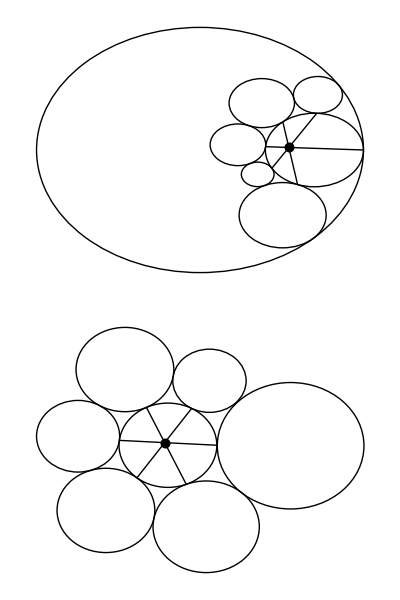

```mathematica
r1={1,.3,.15,.2,.17,.1};
r2={.2,.3,.15,.2,.17,.2};
Column[{
			
Show[Graphics[
		{SevenCircles[r1,-1],PointSize[.02],SevenCirclesPoint[r1,-1]
	}],AspectRatio->Automatic,ImageSize->360],
			
			Show[Graphics[{
		SevenCircles[r2,1],PointSize[.02],SevenCirclesPoint[r2,1]
	}],AspectRatio->Automatic,ImageSize->360]
}]
```

```mathematica
t={{.3,.6},{0,0},{1,0}};
Show[Graphics[{
			SevenCirclesTriangle[t],PointSize[.02],SevenCirclesTrianglePoint[t]
}],AspectRatio->Automatic]
```

Part::partw: Part 2 of Incircle[{{0.3,0.6},{0,0},{1,0}}] does not exist.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Part::partw: Part 3 of CornerCircles[{{{0.3,0.6},{0,0}},Incircle[{{0.3,0.6},{0,0},{1,0}}]⟦2⟧},{{0.3,0.6},{0,0},{1,0}}] does not exist.

Part::partw: Part 2 of Incircle[{{0.3,0.6},{0,0},{1,0}}] does not exist.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

-Graphics-